```mathematica
<<Units`
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
σ=2Pi*α^2/me^2*((1+k)/k^2*((2(1+k))/(1+2k)-Log[1+2k]/k)+Log[1+2k]/(2k)-(1+3k)/(1+2k)^2);
```

```mathematica
Series[σ,{k,0,0}]//Normal
```

(8 π α^2)/(3 me^2)

```mathematica
Series[σ/.k->1/x,{x,0,1}]//Normal
```

```mathematica
(π x α^2 (1+2 Log[2]-2 Log[x]))/(2 me^2)/.x->me/ω//FullSimplify
```

```mathematica
(π α^2 (1+Log[4]+2 Log[ω/me]))/(2 me ω)//FullSimplify
```

(π α^2 (1+Log[4]+2 Log[ω/me]))/(2 me ω)

```mathematica
full=σ/.{k->ω/me}/.{α->1/137,me->0.511};//FullSimplify
```

```mathematica
full*400/.ω->1000
```

0.00114857

```mathematica
Convert[0.008Barn,Milli Barn]
```

8. Barn Milli

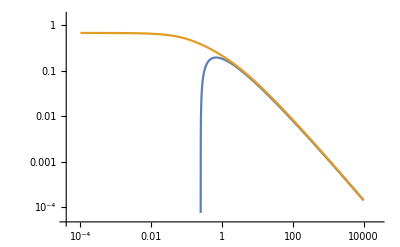

```mathematica
LogLogPlot[{(0.0001673819944370927 (Log[16. ω^2]))/ω*400,full*400},{ω,0.0001,10000}]
```

#### Critical Energy

```mathematica
4 α^3/me^2 Z^2Log[10]*Sqrt[0.1/k]/.{me->0.511,α->1/137,Z->1}
```

4.33783×10^-6 √(1/k)

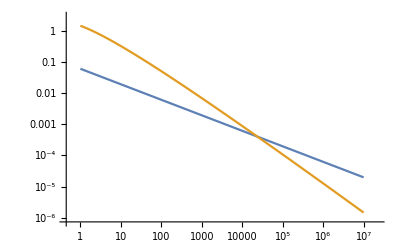

```mathematica
LogLogPlot[{4.3378265073410035*^-6 √(1/k)*6^2*400,(0.0001673819944370927 (1+Log[16. k^2]))/k 6*400},{k,1,10000000}]
```